## VE401 RC 2

## Continuous Random Variables

#### Exponential Distribution

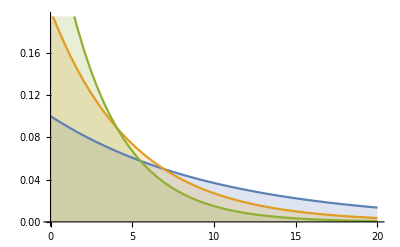

```mathematica
Plot[Table[PDF[ExponentialDistribution[β], x], {β, {0.1, 0.2, 0.3}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Gamma Distribution

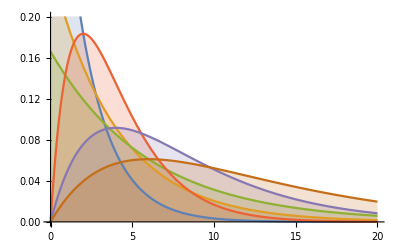

```mathematica
Plot[Table[PDF[GammaDistribution[α, β], x], {α, {1, 2}}, {β, {2, 4, 6}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Chi-Squared Distribution

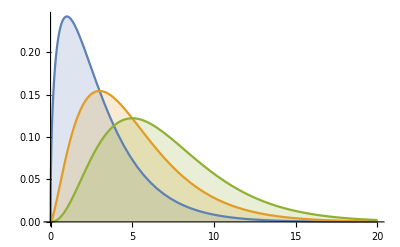

```mathematica
Plot[Table[PDF[ChiSquareDistribution[γ], x], {γ, {3, 5, 7}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Normal Distribution

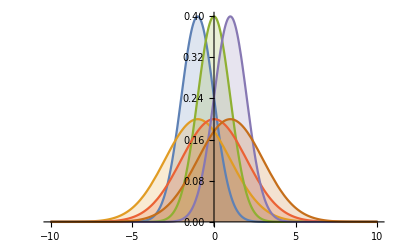

```mathematica
Plot[Table[PDF[NormalDistribution[μ, σ], x], {μ, {-1, 0, 1}}, {σ, {1, 2}}] // Evaluate, {x, -10, 10}, Filling->Axis]
```